```mathematica
Exit[];
```

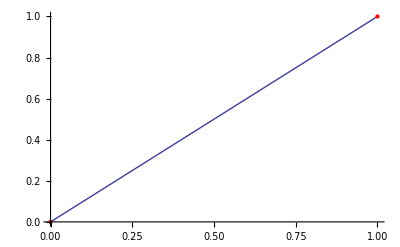

```mathematica
Punkte={0,1};n=Length[Punkte];
x[i_]:=1/(n-1)*(i-1)
L[i_,y_]:=Product[(y-x[j])/(x [i]-x[j]),{j,i-1}]*Product[(y-x[j])/(x [i]-x[j]),{j,i+1,n}]
Show[Plot[Sum[L[i,y]*Punkte[[i]],{i,n}],{y,0,1}],
ListPlot[Table[{x[i],Punkte[[i]]},{i,n}],PlotStyle->Directive[PointSize[Large],Red]]]
```

```mathematica
L[1,y]
L[2,y]
```

1-y

y

```mathematica
h={1,y,y^2,y^3}
```

{1,y,y^2,y^3}

```mathematica
co=Inverse[{{1,0,1,0},{-1,1,1,1},{1,-2,1,2},{-1,3,1,3}}];c//MatrixForm
```

c

```mathematica
co.h
```

{1/2-(3 y)/4+y^3/4,1/4-y/4-y^2/4+y^3/4,1/2+(3 y)/4-y^3/4,-1/4-y/4+y^2/4+y^3/4}

```mathematica
co[[1]]
```

{1/2,-3/4,0,1/4}

```mathematica
H[i_,y_]:=Sum[y^(j-1)*c[[i,j]],{j,4}]
```

```mathematica
H[1,y]
```

1/2-(3 y)/4+y^3/4

```mathematica
tt
```

```mathematica
g[x_]:=Select[tt,Abs[x-#[[1]]]<2/nN&]
```

```mathematica
f[x0_,tt0_,nN0_,co0_]:=Module[{x=x0,y,h,tt=tt0,nN=nN0,co=co0},
S=Select[tt,x==#[[1]]&];
If[Length[S]≠0,
S[[1,2]],
S=Select[tt,Abs[x-#[[1]]]<2/nN&];
h={1,y,y^2,y^3}/.y->(x-#[[2,1]])/(#[[3,1]]-#[[2,1]])&[S];
{#[[2,2]],(#[[3,2]]-#[[1,2]])/2,#[[3,2]],(#[[4,2]]-#[[2,2]])/2}.co.h&[S]]]
```

```mathematica
f[0,tt,nN,co]
```

-0.016

```mathematica
Select[tt,0.020052287581699347==#[[1]]&]
```

{{0.0200523,-0.00906009}}

```mathematica
tt[[2]]
```

{0.0200523,-0.00906009}

```mathematica
g[0.5]
```

{{0.461203,0.000329567},{0.481255,0.000469316},{0.501307,0.00059029},{0.521359,0.00072094}}

```mathematica
tt[[
```

Part::partw: Part 4 of {{0.0601569, -0.00644924}, {« 1 »}, {0.100261, -0.00492535}} does not exist.

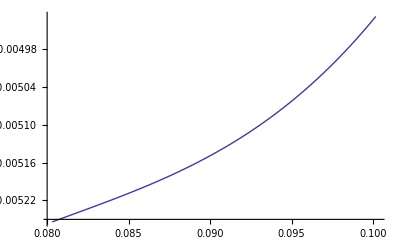

```mathematica
ii=5;Plot[f[tr,tt,nN,co],{tr,tt[[ii,1]],tt[[ii+1,1]]}]
```

```mathematica
Sum[H[i,y]*Punkte[[i]],{i,4}]
```

1/2-(3 y)/4+y^3/4+2 (1/4-y/4-y^2/4+y^3/4)

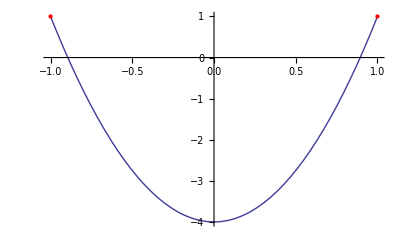

```mathematica
Punkte={1,-10,1,10};
Show[Plot[Sum[H[i,y]*Punkte[[i]],{i,4}],{y,-1,1}],
ListPlot[Table[{2*i-3,Punkte[[2*i-1]]},{i,2}],PlotStyle->Directive[PointSize[Large],Red]]]
```